# Allan Variance for DNA Sequence

## 準備

```mathematica
(*Get["/home/kamano/SCRIPT-MATHEMATICA/SCRIPTS/DNA_sequence_operations.txt"]*)
```

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/DNA_sequence_operations.txt"]
```

## Allan Variance Plot 手順

ベクトル a = {a1,a2,a3...}とする。

時間幅(window の大きさ)wを決定する

ベクトルa より、幅wからなるすべてのサブリストを生成する

すべての隣接するサブリスト(window) 間の平均差をとる

その平均差の値を2 乗したものの平均に、1/2 を掛けた値がAllan Variance と
なる

上記1-4 のステップを、可能なwにつき行う

wを横軸座標に、対応するAllan Variance のルートを縦軸座標に、両対数プロッ
トしたものがAllan Variance Plot である

アランバリアンスの式 :

```mathematica
allanVar[ylist_,w_]:=1/2 Mean[(ListCorrelate[Append[PadRight[{-1},w],1],MovingAverage[ylist,w]])^2]
```

### Plot example (from Wolfram MathSource)

```mathematica
Manipulate[
Module[{Ntot,opts,ylist,g1,g2,Npts,τdata,σdata,στdata},
Ntot=5000;
opts=Sequence[Frame->True,Axes->False,Joined->True,GridLines->Automatic,BaseStyle->12,ImageSize->480];
ylist=RandomReal[NormalDistribution[0,a],Ntot]+b Cos[(2 π)/T Range[Ntot]]+d Range[Ntot];
g1=ListPlot[ylist,FrameLabel->{"t [s]","y(t)"},PlotRange->{All,{-0.4,0.4}},AspectRatio->0.17,opts];
Npts=30;
τdata=Union[ Table[Round[10^((i-1)Log[10,1000]/Npts)],{i,1,Npts+1}]];
σdata=√allanVar[ylist,#]& /@ τdata;
στdata=Transpose[{τdata,σdata}];
g2=Show[
ListLogLogPlot[στdata,PlotMarkers->Automatic,FrameLabel->{"τ [s]","σ_y(τ)"},PlotRange->{All,{0.00009,0.2}},AspectRatio->0.48,opts,FrameTicks->{{1,10,100,1000},{{10^-4,"10^-4"},{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"}},None,None}],
LogLogPlot[b Sin[π τ /T]^2/ (π τ/T),{τ,1,1000},PlotStyle->Directive[{Thick,Dashed,RGBColor[.49,0,0]}]],
LogLogPlot[d τ/√2,{τ,1,1000},PlotStyle->Directive[{Thick,Dashed,Darker@RGBColor[.6,.73,.36]}]]
];
Column[{g1,g2}]
],
{{a,0.05,"white frequency noise amplitude"},0.01,0.1,Appearance->"Labeled"},
{{b,0.012,"oscillation amplitude"},0,0.1,Appearance->"Labeled"},
{{T,100,"oscillation period (s)"},10,1000,Appearance->"Labeled"},
{{d,0.000005,"drift (1/s)"},0,0.0001,Appearance->"Labeled"},
SaveDefinitions->True,TrackedSymbols:>{a,b,T,d}
]
```

## Allan Variance Plot DNA塩基配列への応用手順：オリゴヌクレオチド法

DNA 塩基配列データを、a = {a1,a2,a3...}とする(a1、a2... は、塩基)。

部分塩基配列(window) の大きさw 決定する

全塩基配列データa より、幅w からなるすべての部分塩基配列を生成する

すべての隣接する部分塩基配列(window) 間の距離をとる

部分塩基配列の隣接ペアを作成する

配列の長さをLとすると、ペアなので、wは最大L/2となる。

オリゴヌクレオチド頻度ベクトルを生成し、ベクトルはノルム1にノーマライズする(NEW)

距離はオリゴヌクレオチド頻度ベクトルにおけるユークリッド距離とする

オリゴヌクレオチド頻度は部分配列において取りうるすべてのオリゴヌク
レオチド長n を考える

その距離を2 乗したものの平均に、1/2 を掛けた値がAllan Variance 様値となる

上記1-4 のステップを、可能なw、n につき行う

各nにつき、w を横軸座標に、対応するAllan Variance 様値のルートを縦軸座
標に、両対数プロットしたものがAllan Variance 様Plot となる

#### example

アランバリアンス様値の式 :

DNAシークエンスを用意

```mathematica
dnaseq="AAGTTTCGGGGCATTTTGCCCCA"
```

AAGTTTCGGGGCATTTTGCCCCA

```mathematica
l=Floor[StringLength[dnaseq]/2]
```

11

1. 部分塩基配列 (window) の大きさw 決定する (仮にw=7)

```mathematica
w=7
```

7

2. 全塩基配列データa より、幅w からなるすべての部分塩基配列を生成する

```mathematica
dnasubseqs=seqToSubseqs[dnaseq,w]
```

{AAGTTTC,AGTTTCG,GTTTCGG,TTTCGGG,TTCGGGG,TCGGGGC,CGGGGCA,GGGGCAT,GGGCATT,GGCATTT,GCATTTT,CATTTTG,ATTTTGC,TTTTGCC,TTTGCCC,TTGCCCC,TGCCCCA}

3. すべての隣接する部分塩基配列(window) 間の距離をとる

3.1. すべての隣接配列のペアを生成

```mathematica
cp[7]=contactPair[dnasubseqs,w]
```

{{AAGTTTC,GGGGCAT},{AGTTTCG,GGGCATT},{GTTTCGG,GGCATTT},{TTTCGGG,GCATTTT},{TTCGGGG,CATTTTG},{TCGGGGC,ATTTTGC},{CGGGGCA,TTTTGCC},{GGGGCAT,TTTGCCC},{GGGCATT,TTGCCCC},{GGCATTT,TGCCCCA}}

3.2. オリゴヌクレオチド頻度ベクトルを生成し、ベクトルはノルム1にノーマライズする(仮にn=3)

```mathematica
n=3
```

3

```mathematica
(ov[7,3]=Map[Normalize[oligonucToVec[#,n]]&,cp[w],{2}])//Dimensions
```

{10,2,64}

3.3. 距離はオリゴヌクレオチド頻度ベクトルにおけるユークリッド距離とする

```mathematica
eu[7,3]=Apply[EuclideanDistance,ov[7,3],{1}]
```

{√2,√2,2 √(2/5),√(43/35+(-1/(√5)+2/(√7))^2),√2,√2,√2,√2,√2,√2}

3.4. オリゴヌクレオチド頻度は部分配列において取りうるすべてのオリゴヌク
レオチド長n を考える

4. その距離を2 乗したものの平均に、1/2 を掛けた値がAllan Variance 様値となる

```mathematica
eum[7,3]=N[Mean[eu[7,3]^2]/2]
```

0.946194

1. - 4. を一度に行なう。

```mathematica
AllanDNA[7,3]=Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,3]]&,seqToSubseqs[dnaseq,7]],7]//N]]/2
```

0.946194

5. 上記1-4 のステップを、可能なw、n につき行う

```mathematica
Table[{w,n},{w,1,l},{n,1,w}]
```

{{{1,1}},{{2,1},{2,2}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3},{4,4}},{{5,1},{5,2},{5,3},{5,4},{5,5}},{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6}},{{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7}},{{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8}},{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9}},{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}},{{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11}}}

```mathematica
dnasubseqsALL=Table[seqToSubseqs[dnaseq,w],{w,1,l}]
```

{{A,A,G,T,T,T,C,G,G,G,G,C,A,T,T,T,T,G,C,C,C,C,A},{AA,AG,GT,TT,TT,TC,CG,GG,GG,GG,GC,CA,AT,TT,TT,TT,TG,GC,CC,CC,CC,CA},{AAG,AGT,GTT,TTT,TTC,TCG,CGG,GGG,GGG,GGC,GCA,CAT,ATT,TTT,TTT,TTG,TGC,GCC,CCC,CCC,CCA},{AAGT,AGTT,GTTT,TTTC,TTCG,TCGG,CGGG,GGGG,GGGC,GGCA,GCAT,CATT,ATTT,TTTT,TTTG,TTGC,TGCC,GCCC,CCCC,CCCA},{AAGTT,AGTTT,GTTTC,TTTCG,TTCGG,TCGGG,CGGGG,GGGGC,GGGCA,GGCAT,GCATT,CATTT,ATTTT,TTTTG,TTTGC,TTGCC,TGCCC,GCCCC,CCCCA},{AAGTTT,AGTTTC,GTTTCG,TTTCGG,TTCGGG,TCGGGG,CGGGGC,GGGGCA,GGGCAT,GGCATT,GCATTT,CATTTT,ATTTTG,TTTTGC,TTTGCC,TTGCCC,TGCCCC,GCCCCA},{AAGTTTC,AGTTTCG,GTTTCGG,TTTCGGG,TTCGGGG,TCGGGGC,CGGGGCA,GGGGCAT,GGGCATT,GGCATTT,GCATTTT,CATTTTG,ATTTTGC,TTTTGCC,TTTGCCC,TTGCCCC,TGCCCCA},{AAGTTTCG,AGTTTCGG,GTTTCGGG,TTTCGGGG,TTCGGGGC,TCGGGGCA,CGGGGCAT,GGGGCATT,GGGCATTT,GGCATTTT,GCATTTTG,CATTTTGC,ATTTTGCC,TTTTGCCC,TTTGCCCC,TTGCCCCA},{AAGTTTCGG,AGTTTCGGG,GTTTCGGGG,TTTCGGGGC,TTCGGGGCA,TCGGGGCAT,CGGGGCATT,GGGGCATTT,GGGCATTTT,GGCATTTTG,GCATTTTGC,CATTTTGCC,ATTTTGCCC,TTTTGCCCC,TTTGCCCCA},{AAGTTTCGGG,AGTTTCGGGG,GTTTCGGGGC,TTTCGGGGCA,TTCGGGGCAT,TCGGGGCATT,CGGGGCATTT,GGGGCATTTT,GGGCATTTTG,GGCATTTTGC,GCATTTTGCC,CATTTTGCCC,ATTTTGCCCC,TTTTGCCCCA},{AAGTTTCGGGG,AGTTTCGGGGC,GTTTCGGGGCA,TTTCGGGGCAT,TTCGGGGCATT,TCGGGGCATTT,CGGGGCATTTT,GGGGCATTTTG,GGGCATTTTGC,GGCATTTTGCC,GCATTTTGCCC,CATTTTGCCCC,ATTTTGCCCCA}}

```mathematica
Table[cp[w]=contactPair[dnasubseqsALL[[w]],w],{w,1,l}]
```

{{{A,A},{A,G},{G,T},{T,T},{T,T},{T,C},{C,G},{G,G},{G,G},{G,G},{G,C},{C,A},{A,T},{T,T},{T,T},{T,T},{T,G},{G,C},{C,C},{C,C},{C,C},{C,A}},{{AA,GT},{AG,TT},{GT,TT},{TT,TC},{TT,CG},{TC,GG},{CG,GG},{GG,GG},{GG,GC},{GG,CA},{GC,AT},{CA,TT},{AT,TT},{TT,TT},{TT,TG},{TT,GC},{TG,CC},{GC,CC},{CC,CC},{CC,CA}},{{AAG,TTT},{AGT,TTC},{GTT,TCG},{TTT,CGG},{TTC,GGG},{TCG,GGG},{CGG,GGC},{GGG,GCA},{GGG,CAT},{GGC,ATT},{GCA,TTT},{CAT,TTT},{ATT,TTG},{TTT,TGC},{TTT,GCC},{TTG,CCC},{TGC,CCC},{GCC,CCA}},{{AAGT,TTCG},{AGTT,TCGG},{GTTT,CGGG},{TTTC,GGGG},{TTCG,GGGC},{TCGG,GGCA},{CGGG,GCAT},{GGGG,CATT},{GGGC,ATTT},{GGCA,TTTT},{GCAT,TTTG},{CATT,TTGC},{ATTT,TGCC},{TTTT,GCCC},{TTTG,CCCC},{TTGC,CCCA}},{{AAGTT,TCGGG},{AGTTT,CGGGG},{GTTTC,GGGGC},{TTTCG,GGGCA},{TTCGG,GGCAT},{TCGGG,GCATT},{CGGGG,CATTT},{GGGGC,ATTTT},{GGGCA,TTTTG},{GGCAT,TTTGC},{GCATT,TTGCC},{CATTT,TGCCC},{ATTTT,GCCCC},{TTTTG,CCCCA}},{{AAGTTT,CGGGGC},{AGTTTC,GGGGCA},{GTTTCG,GGGCAT},{TTTCGG,GGCATT},{TTCGGG,GCATTT},{TCGGGG,CATTTT},{CGGGGC,ATTTTG},{GGGGCA,TTTTGC},{GGGCAT,TTTGCC},{GGCATT,TTGCCC},{GCATTT,TGCCCC},{CATTTT,GCCCCA}},{{AAGTTTC,GGGGCAT},{AGTTTCG,GGGCATT},{GTTTCGG,GGCATTT},{TTTCGGG,GCATTTT},{TTCGGGG,CATTTTG},{TCGGGGC,ATTTTGC},{CGGGGCA,TTTTGCC},{GGGGCAT,TTTGCCC},{GGGCATT,TTGCCCC},{GGCATTT,TGCCCCA}},{{AAGTTTCG,GGGCATTT},{AGTTTCGG,GGCATTTT},{GTTTCGGG,GCATTTTG},{TTTCGGGG,CATTTTGC},{TTCGGGGC,ATTTTGCC},{TCGGGGCA,TTTTGCCC},{CGGGGCAT,TTTGCCCC},{GGGGCATT,TTGCCCCA}},{{AAGTTTCGG,GGCATTTTG},{AGTTTCGGG,GCATTTTGC},{GTTTCGGGG,CATTTTGCC},{TTTCGGGGC,ATTTTGCCC},{TTCGGGGCA,TTTTGCCCC},{TCGGGGCAT,TTTGCCCCA}},{{AAGTTTCGGG,GCATTTTGCC},{AGTTTCGGGG,CATTTTGCCC},{GTTTCGGGGC,ATTTTGCCCC},{TTTCGGGGCA,TTTTGCCCCA}},{{AAGTTTCGGGG,CATTTTGCCCC},{AGTTTCGGGGC,ATTTTGCCCCA}}}

```mathematica
cp[11]
```

{{AAGTTTCGGGG,CATTTTGCCCC},{AGTTTCGGGGC,ATTTTGCCCCA}}

```mathematica
AbsoluteTiming[Timing[Table[ov[w,n]=Map[Normalize[N[oligonucToVec[#,n]]]&,cp[w],{2}],{w,1,l},{n,1,w}];]]
```

{87.3474,{86.7008,Null}}

```mathematica
AbsoluteTiming[Timing[ParallelTable[ov[w,n]=Map[Normalize[N[oligonucToVec[#,n]]]&,cp[w],{2}],{w,1,l},{n,1,w}];]]
```

{60.7392,{7.72783,Null}}

```mathematica
Table[eu[w,n]=Apply[EuclideanDistance,ov[w,n],{1}],{w,1,l},{n,1,w}];
```

```mathematica
eu[22,1]
```

eu[22,1]

```mathematica
Table[eum[w,n]=N[Mean[eu[w,n]^2]/2],{w,1,l},{n,1,w}]
```

{{0.454545},{0.567157,0.85},{0.623459,0.916667,1.},{0.644423,0.958333,1.,1.},{0.607598,0.931848,1.,1.,1.},{0.492806,0.869208,1.,1.,1.,1.},{0.341362,0.766108,0.946194,1.,1.,1.,1.},{0.245926,0.667217,0.875748,1.,1.,1.,1.,1.},{0.214534,0.627385,0.841934,1.,1.,1.,1.,1.,1.},{0.264885,0.612393,0.802811,1.,1.,1.,1.,1.,1.,1.},{0.351582,0.673363,0.832752,1.,1.,1.,1.,1.,1.,1.,1.}}

## Allan Variance Plot DNA塩基配列への応用例

### PolyA

```mathematica
testSeqPolyA=StringJoin[Table["A",{500}]];
```

```mathematica
AbsoluteTiming[AllanDNA["A",100,5]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyA,w]],w]//N]]/2,{w,10,100,10},{n,1,5}]]]
```

{3.24145,{{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}}

### PolyACGT

```mathematica
testSeqPolyACGT=StringJoin[Table["ACGT",{500}]];
```

長さ500*4のシークエンス
w: 4から16
n: 1から4

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,4]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,4,16,1},{n,1,4}]]]
```

{139.204,{{0.,0.,0.,0.},{0.142857,0.,0.333333,0.5},{0.2,0.142857,0.,0.333333},{0.0769231,0.1,0.142857,0.},{0.,0.,0.,0.},{0.047619,0.,0.0769231,0.1},{0.0769231,0.047619,0.,0.0769231},{0.0322581,0.0384615,0.047619,0.},{0.,0.,0.,0.},{0.0232558,0.,0.0322581,0.0384615},{0.04,0.0232558,0.,0.0322581},{0.0175439,0.02,0.0232558,0.},{0.,0.,0.,0.}}}

```mathematica
AllanDNA["ACGT",4,16,1,4]//TableForm
```

0. | 0. | 0. | 0.
0.142857 | 0. | 0.333333 | 0.5
0.2 | 0.142857 | 0. | 0.333333
0.0769231 | 0.1 | 0.142857 | 0.
0. | 0. | 0. | 0.
0.047619 | 0. | 0.0769231 | 0.1
0.0769231 | 0.047619 | 0. | 0.0769231
0.0322581 | 0.0384615 | 0.047619 | 0.
0. | 0. | 0. | 0.
0.0232558 | 0. | 0.0322581 | 0.0384615
0.04 | 0.0232558 | 0. | 0.0322581
0.0175439 | 0.02 | 0.0232558 | 0.
0. | 0. | 0. | 0.

```mathematica
ListPlot3D[AllanDNA["ACGT",4,16,1,4]]
```

-Graphics3D-

```mathematica
AbsoluteTiming[AllanDNA["ACGT",5,16,5,5]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,5,16},{n,5,5}]]]
```

{423.02,{{1.},{1.},{0.333333},{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.}}}

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,1]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,4,16,1},{n,1,1}]]]
```

{0.650949,{{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.},{0.0232558},{0.04},{0.0175439},{0.}}}

```mathematica
AllanDNA["ACGT",4,16,1,1]
```

{{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.},{0.0232558},{0.04},{0.0175439},{0.}}

### Random

```mathematica
(testseqRandom=StringJoin[Table[RandomInteger[{1,4}],{4000}]/.{1->"A",2->"C",3->"G",4->"T"}])//StringLength
```

4000

長さ4000のシークエンス
w: 2,3
n: 1から3

```mathematica
AbsoluteTiming[AllanDNA["Random",2,3,1,2]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testseqRandom,w]],w]//N]]/2,{w,2,3},{n,1,2}]]]
```

{6.6252,{{0.578257,0.941206},{0.466536,0.886183}}}

```mathematica
AbsoluteTiming[AllanDNA["Random",3,3,3,3]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testseqRandom,w]],w]//N]]/2,{w,3,3},{n,3,3}]]]
```

{0.887851,{{0.985232}}}

```mathematica
AllanDNA["Random",2,3,1,3]=Map[PadRight[#,4]&,Insert[AllanDNA["Random",2,3,1,2],AllanDNA["Random",3,3,3,3][[1,1]],{2,3}]]
```

{{0.578257,0.941206,0,0},{0.466536,0.886183,0.985232,0}}

長さ4000のシークエンス
w: 4から16
n: 1から4

```mathematica
AbsoluteTiming[AllanDNA["Random",4,16,1,4]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testseqRandom,w]],w]//N]]/2,{w,4,16,1},{n,1,4}]]]
```

{271.418,{{0.389255,0.828839,0.968445,0.995743},{0.339796,0.776535,0.949547,0.9891},{0.304265,0.734811,0.933396,0.983131},{0.275215,0.698302,0.919842,0.97883},{0.253342,0.666404,0.908677,0.9771},{0.234076,0.636894,0.896517,0.97425},{0.216097,0.608962,0.88467,0.971768},{0.200924,0.583534,0.872486,0.969154},{0.187139,0.559851,0.860359,0.966294},{0.175151,0.537681,0.847862,0.963075},{0.164815,0.517793,0.836659,0.96003},{0.155287,0.500383,0.82613,0.957388},{0.146839,0.484095,0.816407,0.954767}}}

```mathematica
AllanDNA["Random",4,16,1,4]//TableForm
```

0.389255 | 0.828839 | 0.968445 | 0.995743
0.339796 | 0.776535 | 0.949547 | 0.9891
0.304265 | 0.734811 | 0.933396 | 0.983131
0.275215 | 0.698302 | 0.919842 | 0.97883
0.253342 | 0.666404 | 0.908677 | 0.9771
0.234076 | 0.636894 | 0.896517 | 0.97425
0.216097 | 0.608962 | 0.88467 | 0.971768
0.200924 | 0.583534 | 0.872486 | 0.969154
0.187139 | 0.559851 | 0.860359 | 0.966294
0.175151 | 0.537681 | 0.847862 | 0.963075
0.164815 | 0.517793 | 0.836659 | 0.96003
0.155287 | 0.500383 | 0.82613 | 0.957388
0.146839 | 0.484095 | 0.816407 | 0.954767

長さ4000のシークエンス、Allan分散の合成。ゼロパディング。
w: 2から16
n: 1から4

```mathematica
(AllanDNA["Random",2,16,1,4]=Join[AllanDNA["Random",2,3,1,3],AllanDNA["Random",4,16,1,4]])//Dimensions
```

{15,4}

```mathematica
ListPlot3D[AllanDNA["Random",2,16,1,4]]
```

-Graphics3D-

```mathematica
AbsoluteTiming[AllanDNA["ACGT",5,16,5,5]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,5,16},{n,5,5}]]]
```

{422.279,{{1.},{1.},{0.333333},{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.}}}

```mathematica
AbsoluteTiming[AllanDNA["ACGT",5,16,5,5]=Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,5,16},{n,5,5}]]
```

{1582.81,{{1.},{1.},{0.333333},{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.}}}

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,1]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,4,16,1},{n,1,1}]]]
```

{0.664083,{{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.},{0.0232558},{0.04},{0.0175439},{0.}}}

```mathematica
AllanDNA["ACGT",4,16,1,1]
```

{{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.},{0.0232558},{0.04},{0.0175439},{0.}}

## Allan Variance Plot DNA塩基配列への応用手順：複素数法

### PolyACGT

```mathematica
allanVar[ylist_,w_]:=1/2 Mean[(ListCorrelate[Append[PadRight[{-1},w],1],MovingAverage[ylist,w]])^2]
```

```mathematica
allanVar[{I,I,I,I,I,I,I,I,1,1,1,1},2]//Abs
```

1/6

```mathematica
allanVar[{I,I,I,I,I,I,I,I,1,1,1,1},4]//Abs
```

3/8

```mathematica
allanVar[{I,1,I,1,I,1,I,1,I,I,-1},2]//Abs
```

(√5)/32

```mathematica
allanVar[{I,1,I,1,I,1,I},2]//Abs
```

0

```mathematica
testSeqPolyACGT=StringJoin[Table["ACGT",{500}]];
```

長さ500*4のシークエンス
w: 4から16
n: 1から4

```mathematica
testSeqPolyACGTcomp=N[nucleotideToComplex[testSeqPolyACGT]];
```

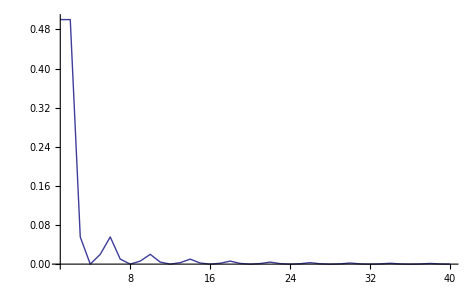

```mathematica
ListPlot[Table[allanVar[testSeqPolyACGTcomp,n]//Abs,{n,1,40}],PlotRange->All,Joined->True]
```

## Mathematica Script作成

dir:
/home/kamano/TEST_COLLECTION/AllanVarianceLike-Plot/bin/

アウトプット:
*.out.list

条件:
(window size;oligonucleotide length): 4-128;1-4(que[1]), 129-256;1-4(que[2]), 257-384;1-4(que[3]), 385-512;1-4(que[4]).